```mathematica
ρ={x*(x-1)*y*(y-1),x^2*(x-1)*y*(y-1),x*(x-1)*y^2*(y-1),x^2*(x-1)*y^2*(y-1)}
k=Table[Integrate[Integrate[Grad[ρ[[m]],{x,y}].Grad[ρ[[n]],{x,y}]+ρ[[m]]*ρ[[n]],{y,0,1}],{x,0,1}],{m,4},{n,4}]
```

{(-1+x) x (-1+y) y,(-1+x) x^2 (-1+y) y,(-1+x) x (-1+y) y^2,(-1+x) x^2 (-1+y) y^2}

{{7/300,7/600,7/600,7/1200},{7/600,1/126,7/1200,1/252},{7/600,7/1200,1/126,1/252},{7/1200,1/252,1/252,29/11025}}

```mathematica
f=Table[Integrate[Integrate[(2*Pi^2+1)*Sin[Pi*x]*Sin[Pi*y]*ρ[[n]],{y,0,1}],{x,0,1}],{n,4}]
```

{(16+32 π^2)/π^6,(8+16 π^2)/π^6,(8+16 π^2)/π^6,(4+8 π^2)/π^6}

```mathematica
Mean[f]
```

1/4 ((4+8 π^2)/π^6+(2 (8+16 π^2))/π^6+(16+32 π^2)/π^6)

```mathematica
W=LinearSolve[k,f]
```

{(4800 (1+2 π^2))/(7 π^6),0,0,0}

```mathematica
Uh[x_,y_]:=W.ρ
```

```mathematica
Uh[x,y]
```

(4800 (1+2 π^2) (-1+x) x (-1+y) y)/(7 π^6)

```mathematica
G1=Plot3D[Uh[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
G2=Plot3D[Sin[Pi*x]*Sin[Pi*y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Show[G1,G2,PlotRange->All]
```

-Graphics3D-

```mathematica
k//MatrixForm
```

(7/300 | 7/600 | 7/600 | 7/1200
7/600 | 1/126 | 7/1200 | 1/252
7/600 | 7/1200 | 1/126 | 1/252
7/1200 | 1/252 | 1/252 | 29/11025)

```mathematica
f//MatrixForm
```

((16+32 π^2)/π^6
(8+16 π^2)/π^6
(8+16 π^2)/π^6
(4+8 π^2)/π^6)

```mathematica
Plot3D[Uh[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[Pi*x]*Sin[Pi*y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Sin[Pi*x]*Sin[Pi*y]
```

## Lista 3- Questão 4b)

```mathematica
B={Sin[Pi*x]*Sin[Pi*y]}
```

{Sin[π x] Sin[π y]}

```mathematica
F=Integrate[Integrate[(2*Pi^2+1)*Sin[Pi*x]*Sin[Pi*y]*Sin[Pi*x]*Sin[Pi*y],{y,0,1}],{x,0,1}]
```

1/4 (1+2 π^2)

```mathematica
K=Integrate[Integrate[Grad[Sin[Pi*x]*Sin[Pi*y],{x,y}].Grad[Sin[Pi*x]*Sin[Pi*y],{x,y}]+(Sin[Pi*x]*Sin[Pi*y])^2,{y,0,1}],{x,0,1}]
```

1/4 (1+2 π^2)

```mathematica
Solve[K*w==F,w]
```

{{w→1}}

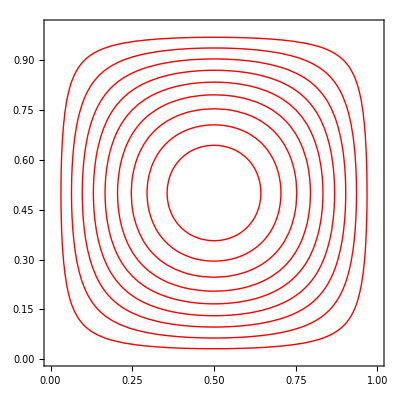

```mathematica
G21=ContourPlot[Sin[Pi*x]*Sin[Pi*y],{x,0,1},{y,0,1},ContourShading->None,ContourStyle->Red]
```

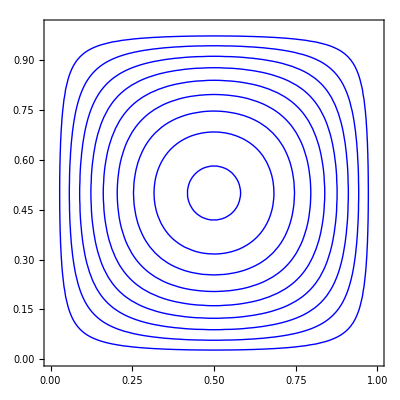

```mathematica
G23=ContourPlot[Uh[x,y],{x,0,1},{y,0,1},ContourShading->None,ContourStyle->Blue]
```

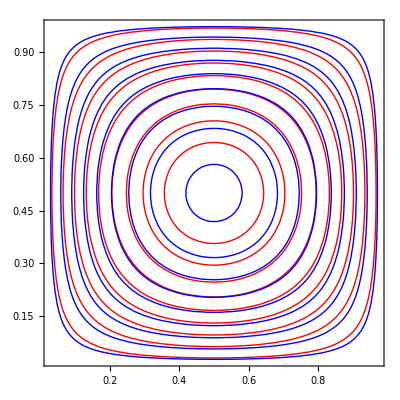

```mathematica
G77=Show[G21,G23,PlotRange->All,ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["g2.png",G77]
```

g2.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g2.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g2.png"]]]
```

```mathematica
G5=Plot3D[{Uh[x,y],Sin[Pi*x]*Sin[Pi*y]},{x,0,1},{y,0,1},ImageSize->400,AxesStyle->Black,PlotLegends->{"Galerkin","Exata"}]
```

-Graphics3D-

```mathematica
Export["g1.png",G5]
```

g1.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g1.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g1.png"]]]
```

```mathematica
ContourPlot[{Uh[x,y],Sin[Pi*x]*Sin[Pi*y]},{x,0,1},{y,0,1},ContourShading->None]
```

ContourPlot::nonopt: Options expected (instead of {y,0,1}) beyond position 3 in ContourPlot[Uh[x,y],Sin[π x] Sin[π y],{x,0,1},{y,0,1},ContourShading→None]. An option must be a rule or a list of rules.

ContourPlot[Uh[x,y],Sin[π x] Sin[π y],{x,0,1},{y,0,1},ContourShading→None]

```mathematica
K2=Integrate[Integrate[Grad[Sin[Pi*x]*Sin[Pi*y],{x,y}].Grad[Sin[Pi*x]*Sin[Pi*y],{x,y}]+Sin[Pi*x]*Sin[Pi*y]*Sin[Pi*x]*Sin[Pi*y],{x,0,1}],{y,0,1}]
```

1/4 (1+2 π^2)

```mathematica
F2=Integrate[Integrate[(2*Pi^2+1)*Sin[Pi*x]*Sin[Pi*y]*Sin[Pi*x]*Sin[Pi*y],{x,0,1}],{y,0,1}]
```

1/4 (1+2 π^2)

```mathematica
Solve[K2*w1==F2,w1]
```

{{w1→1}}

```mathematica
Uh1[x_,y_]:=1.Sin[Pi*x]*Sin[Pi*y]
```

```mathematica
G55=Plot3D[Uh1[x,y],{x,0,1},{y,0,1},ImageSize->400,AxesStyle->Black]
```

-Graphics3D-

```mathematica
Export["4b.png",G55]
```

4b.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["4b.png"]]]
```